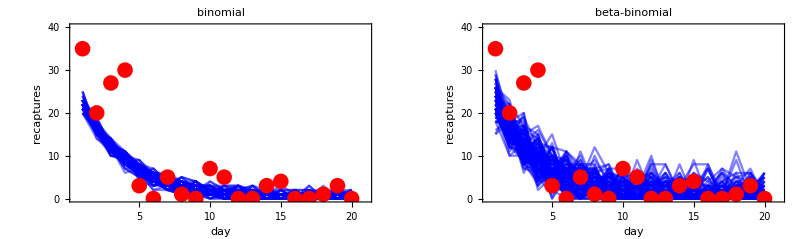

```mathematica
SetDirectory[NotebookDirectory[]];
ClearAll["Global`*"];
fActual[n_,λ_,σ_]:=Module[{noise = RandomVariate[NormalDistribution[0,σ],{20}],recaptures},recaptures=Table[Round@(n PDF[ExponentialDistribution[λ],x] + +noise[[x]]+(1/(0.1x)) noise[[x]]),{x,1,20,1}];If[#>0,#,0]&/@recaptures]
fReplicates[n_,λ_,σ_]:=Module[{noise = RandomVariate[NormalDistribution[0,σ],{20}],recaptures},recaptures=Table[Round@(n PDF[ExponentialDistribution[λ],x] +  noise[[x]]),{x,1,20,1}];If[#>0,#,0]&/@recaptures]
data = fActual[100,0.3,3];
```

```mathematica
data={35,20,27,30,3,0,5,1,0,7,5,0,0,3,4,0,0,1,3,0};
```

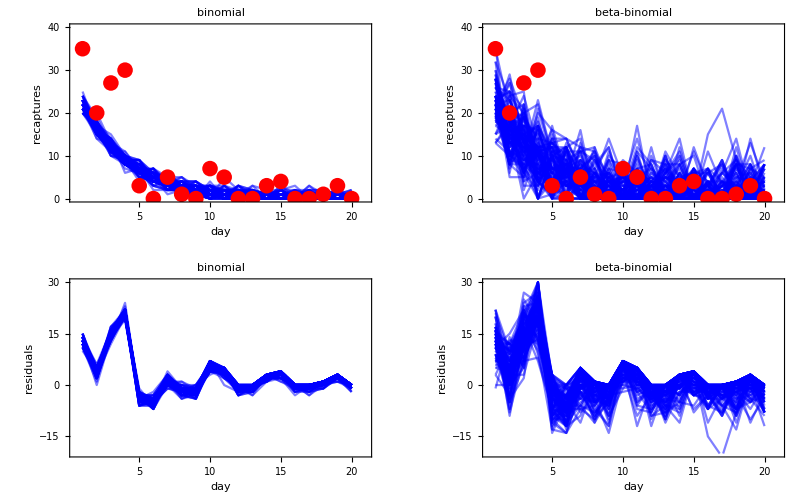

```mathematica
dataFakeBinomial = Table[fReplicates[100,0.3,1],{i,1,100,1}];
dataFakeBetaBinomial =Table[fReplicates[100,0.3,5],{i,1,100,1}];
g1=Show[ListLinePlot[dataFakeBinomial,PlotStyle->Opacity[0.5,Blue],PlotRange->{{0.5,21},{0,Max@data+5}}],ListPlot[data,PlotStyle->Red,PlotMarkers->{●,16}],Frame->{True,True,False,False},FrameLabel->{"day","recaptures"},BaseStyle->{FontSize->16},PlotLabel->"binomial"];
g2=Show[ListLinePlot[dataFakeBetaBinomial,PlotStyle->Opacity[0.5,Blue],PlotRange->{{0.5,21},{0,Max@data+5}}],ListPlot[data,PlotStyle->Red,PlotMarkers->{●,16}],Frame->{True,True,False,False},FrameLabel->{"day","recaptures"},BaseStyle->{FontSize->16},PlotLabel->"beta-binomial"];
residualBinomial = data -#&/@dataFakeBinomial;
residualBetaBinomial = data - #&/@dataFakeBetaBinomial;
g3 = ListLinePlot[residualBinomial,PlotStyle->Opacity[0.5,Blue],PlotRange->{{0.5,21},{-20,30}},Frame->{True,True,False,False},FrameLabel->{"day","residuals"},BaseStyle->{FontSize->16},PlotLabel->"binomial"];
g4 = ListLinePlot[residualBetaBinomial,PlotStyle->Opacity[0.5,Blue],PlotRange->{{0.5,21},{-20,30}},Frame->{True,True,False,False},FrameLabel->{"day","residuals"},BaseStyle->{FontSize->16},PlotLabel->"beta-binomial"];
gFinal=Show[GraphicsGrid[{{g1,g2},{g3,g4}}],ImageSize->800]
```

```mathematica
Export["Evaluation_mosquitoPPC.pdf",gFinal]
```

Evaluation_mosquitoPPC.pdf